```mathematica
(* Simple 1ccp fit to lattice gluon prop *)
```

```mathematica
(* Gluon prop values from Aguilar & Papavassiliou 1010.5815.pdf    Appears to be quenched data ie N_f = 0   So a more realistic prop is smaller at q2=0 and would have a gluon mass fn at q2=0 that is bigger eg 0.5GeV    The 2014+ works of Aguilar et al use the more realistic unquenched N_f = 3 lattice data   *)
```

```mathematica
MG2[q2_]:=  mg^4/(q2 + ρ2*mg^2)
```

```mathematica
zg[q2_]:=1+ (13*CA*g12/(96*π^2)) Log[(q2+ρ1*MG2[q2])/μ^2]
```

```mathematica
params={CA->3,μ->4.3,mg->0.52,g12->5.68,ρ1->8.55,ρ2->1.91}
```

{CA→3,μ→4.3,mg→0.52,g12→5.68,ρ1→8.55,ρ2→1.91}

```mathematica
delta[q2_]:=1/(q2*zg[q2]+MG2[q2])
```

```mathematica
delta[0.0]/.params
```

7.06361

```mathematica
Sqrt[MG2[0.0]/.params]
```

0.376259

```mathematica
(* ****************** fit to 1 complx conj mass pair ******************** *)
```

```mathematica
deltafit1[q2_]:=(zr+I*zi)/(q2+m2r + I*m2i) +(zr-I*zi)/(q2+m2r - I*m2i)
```

```mathematica
Simplify[deltafit1[0]](* = 1/MG2[0] *)
```

(2 (m2i zi+m2r zr))/(m2i^2+m2r^2)

```mathematica
q2pts=Table[q2i,{q2i,0.2,1.8,0.2}  ]
```

{0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8}

```mathematica
nq2=Length[q2pts]
```

9

```mathematica
dataTAB=Table[delta[q2pts[[i]]]/.params,{i,1,nq2}  ]
```

{5.92006,4.66539,3.60914,2.81433,2.23778,1.81931,1.51062,1.27801,1.09886}

```mathematica
fitformTAB=Table[deltafit1[q2pts[[i]]], {i,1,nq2} ];
```

```mathematica
chifit1=( Sum[ (dataTAB[[i]]-fitformTAB[[i]])^2,{i,1,nq2}]/nq2 )^0.5;
```

```mathematica
fit1=FindMinimum[{chifit1,m2r>0.14,m2i>0.01},{m2r,m2i,zr,zi}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {4.25307×10^-13, 0.0127052, 2.53957×10^-13}, is returned.

{0.0136238,{m2r→0.280885,m2i→0.735361,zr→0.211883,zi→2.97439}}

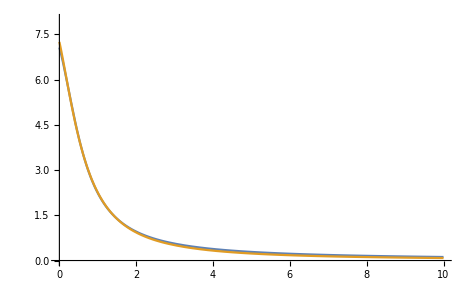

```mathematica
Plot[{delta[q2]/.params,deltafit1[q2]/.fit1[[2]]},{q2,0,10},PlotRange->{{0,10},{0,8}}]
```

```mathematica
Sqrt[m2r+I*m2i]/.fit1[[2]]
```

0.730776+0.503138 ⅈ

```mathematica
(* Can use this as a typical dynamical boson propagator Delta(q2) fit by 1 ccp to explore if it introduces any negative pressure P(T) regions when T is introduced by Matsubara in the mean field  term  -TrLn [ Delta ] for ln[Z] *)
```